```mathematica
ϑ = .2;
Subscript[u, 0]= 1+ϑ;
f[u_,α_]=(u^(α+1)-1)/(α(α+1))-1/α u+1/α;
fs[u_,α_]=Normal[Series[f[u, α],{u,Subscript[u, 0],2}]];
mf[u_,α_]=Piecewise[{{f[u,α],u<Subscript[u, 0]},{fs[u,α],u>=Subscript[u, 0]}}];
```

## Check plain Cressie Read Divergence

```mathematica
f2 =  Table[f[z,2],{z, 0,3,.1}]
```

{0.333333,0.2835,0.234667,0.187833,0.144,0.104167,0.0693333,0.0405,0.0186667,0.00483333,0.,0.00516667,0.0213333,0.0495,0.0906667,0.145833,0.216,0.302167,0.405333,0.5265,0.666667,0.826833,1.008,1.21117,1.43733,1.6875,1.96267,2.26383,2.592,2.94817,3.33333}

```mathematica
f05 =  Table[f[z,.5],{z, 0,3,.1}]
```

```mathematica
fm05 =  Table[f[z,-.5],{z, 0,3,.1}]
```

{2.,0.935089,0.611146,0.40911,0.270178,0.171573,0.101613,0.0533599,0.0222912,0.00526681,0.,0.00476461,0.0182195,0.0392983,0.0671362,0.101021,0.140356,0.184638,0.233437,0.28638,0.343146,0.403449,0.467041,0.5337,0.603227,0.675445,0.750194,0.827329,0.90672,0.988245,1.0718}

## Check Gradient of plain Cressie Read

```mathematica
Table[D[f[z,2],z]/.z->j,{j,0,3,.1}];
```

```mathematica
Table[D[f[z,.5],z]/.z->j,{j,0,3,.1}]
```

```mathematica
Table[D[f[z,-.5],z]/.z->j,{j,0,3,.1}];
```

## Check hessian of Cressie Read

```mathematica
Table[D[f[z,2],{z,2}]/.z->j,{j,0,3,.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
Table[D[f[z,.5],{z,2}]/.z->j,{j,0,3,.1}]
```

Power::infy: Infinite expression 1/0.^0.5 encountered.

{ComplexInfinity,3.16228,2.23607,1.82574,1.58114,1.41421,1.29099,1.19523,1.11803,1.05409,1.,0.953463,0.912871,0.877058,0.845154,0.816497,0.790569,0.766965,0.745356,0.725476,0.707107,0.690066,0.6742,0.65938,0.645497,0.632456,0.620174,0.608581,0.597614,0.58722,0.57735}

```mathematica
Table[D[f[z,-.5],{z,2}]/.z->j,{j,0,3,.1}]
```

Power::infy: Infinite expression 1/0.^1.5 encountered.

{ComplexInfinity,31.6228,11.1803,6.08581,3.95285,2.82843,2.15166,1.70747,1.39754,1.17121,1.,0.866784,0.760726,0.67466,0.603682,0.544331,0.494106,0.451156,0.414087,0.38183,0.353553,0.328603,0.306454,0.286687,0.268957,0.252982,0.238528,0.2254,0.213434,0.20249,0.19245}

## Check modified Cressie-Read

```mathematica
f2 =  Table[mf[z,2],{z, 0,3,.1}]
```

{0.333333,0.2835,0.234667,0.187833,0.144,0.104167,0.0693333,0.0405,0.0186667,0.00483333,0.,0.00516667,0.0213333,0.0493333,0.0893333,0.141333,0.205333,0.281333,0.369333,0.469333,0.581333,0.705333,0.841333,0.989333,1.14933,1.32133,1.50533,1.70133,1.90933,2.12933,2.36133}

```mathematica
fm05 =  Table[mf[z,-.5],{z, 0,3,.1}]
```

{2.,0.935089,0.611146,0.40911,0.270178,0.171573,0.101613,0.0533599,0.0222912,0.00526681,0.,0.00476461,0.0182195,0.039449,0.0682857,0.10473,0.148781,0.200439,0.259705,0.326578,0.401058,0.483146,0.572841,0.670143,0.775052,0.887568,1.00769,1.13542,1.27076,1.41371,1.56426}

## Check gradient modified Cressie-Read

```mathematica
Table[D[mf[z,2],z]/.z->j,{j,0,3,.101}]
```

{-0.5,-0.494899,-0.479598,-0.454096,-0.418392,-0.372487,-0.316382,-0.250075,-0.173568,-0.0868595,0.01005,0.117161,0.2344,0.3556,0.4768,0.598,0.7192,0.8404,0.9616,1.0828,1.204,1.3252,1.4464,1.5676,1.6888,1.81,1.9312,2.0524,2.1736,2.2948}

```mathematica
Table[D[mf[z,-.5],z]/.z->j,{j,0,3,.101}]
```

Power::infy: Infinite expression 1/√0. encountered.

{ComplexInfinity,-4.29317,-2.44994,-1.63336,-1.14658,-0.81439,-0.569175,-0.378594,-0.224971,-0.0977226,0.00992562,0.102539,0.183387,0.26022,0.337053,0.413887,0.49072,0.567553,0.644387,0.72122,0.798053,0.874887,0.95172,1.02855,1.10539,1.18222,1.25905,1.33589,1.41272,1.48955}

## Check hessian Cressie-Read

```mathematica
Table[D[mf[z,3],{z,2}]/.z->j,{j,0,3,.101}]
```

```mathematica
Table[D[mf[z,-1/3],{z,2}]/.z->j,{j,0,3,.101}]
```

## Check Kullback Leibler

```mathematica
ϑ = .2;
Subscript[u, 0]= 1+ϑ;
f[u_]=u*Log[u]-u+1;
fs[u_]=Normal[Series[f[u],{u,Subscript[u, 0],2}]];
mf[u_]=Piecewise[{{f[u],u<Subscript[u, 0]},{fs[u],u>=Subscript[u, 0]}}];
```

```mathematica
Table[f[z],{z, 0,3,.1}]


Table[D[f[z],z]/.z->j,{j,0,3,.1}]
```

```mathematica
Table[D[f[z],{z,2}]/.z->j,{j,0,3,.1}]
```

## Check Modified Kullback Leibler

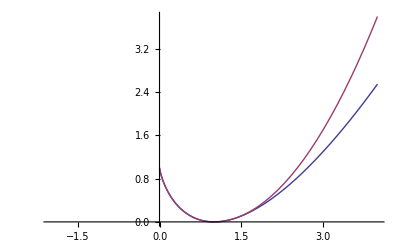

```mathematica
Plot[{f[u],mf[u]},{u,-2,4}]
```

```mathematica
Table[mf[z],{z, 0,3,.1}]
```

```mathematica
Table[D[mf[z],z]/.z->j,{j,0,3,.11}]
```

{Indeterminate,-2.20727,-1.51413,-1.10866,-0.820981,-0.597837,-0.415515,-0.261365,-0.127833,-0.0100503,0.0953102,0.190655,0.282322,0.373988,0.465655,0.557322,0.648988,0.740655,0.832322,0.923988,1.01565,1.10732,1.19899,1.29065,1.38232,1.47399,1.56565,1.65732}

```mathematica
Table[D[mf[z],{z,2}]/.z->j,{j,0,3,.11}]
```

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,9.09091,4.54545,3.0303,2.27273,1.81818,1.51515,1.2987,1.13636,1.0101,0.909091,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333}

```mathematica
{334}
```

```mathematica
D[mf[x],x]/.x->1.3
```

0.265655

## Reverse Kullback-Leibler

```mathematica
ϑ = .2;
Subscript[u, 0]= 1+ϑ;
f[u_]=-Log[u]+u-1;
fs[u_]=Normal[Series[f[u],{u,Subscript[u, 0],2}]];
mf[u_]=Piecewise[{{f[u],u<Subscript[u, 0]},{fs[u],u>=Subscript[u, 0]}}];
```

```mathematica
Table[mf[z],{z, 0,3,.1}]
```

{Indeterminate,1.40259,0.809438,0.503973,0.316291,0.193147,0.110826,0.0566749,0.0231436,0.00536052,0.,0.00468982,0.0176784,0.0378173,0.0649007,0.0989284,0.139901,0.187817,0.242678,0.304484,0.373234,0.448928,0.531567,0.621151,0.717678,0.821151,0.931567,1.04893,1.17323,1.30448,1.44268}

```mathematica
Table[D[mf[z],z]/.z->j,{j,0,3,.11}]
```

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,-8.09091,-3.54545,-2.0303,-1.27273,-0.818182,-0.515152,-0.298701,-0.136364,-0.010101,0.0909091,0.173611,0.25,0.326389,0.402778,0.479167,0.555556,0.631944,0.708333,0.784722,0.861111,0.9375,1.01389,1.09028,1.16667,1.24306,1.31944,1.39583}

```mathematica
Table[D[mf[z],{z,2}]/.z->j,{j,0,3,.11}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

{Indeterminate,82.6446,20.6612,9.18274,5.16529,3.30579,2.29568,1.68663,1.29132,1.0203,0.826446,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444,0.694444}